# 30 Vertices 40 Edges Sporadic Example

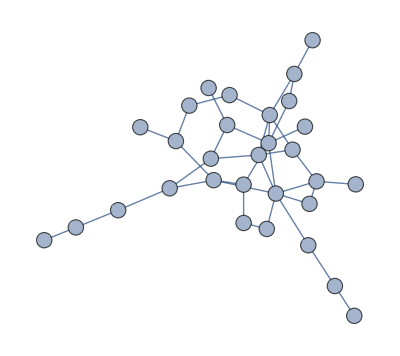

```mathematica
While@Not@ConnectedGraphQ[d=RandomGraph[{30,40},VertexLabels-> Placed[Automatic,Center],VertexSize->1]]
d
```

```mathematica
k=3;

vert=VertexList[d];
absvert=Length[vert];

edge=EdgeList[d];
edge=List @@@%;
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]]

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpolyd=Join[vertpoly,edgepoly];

{dgraphtime,dgrob}=AbsoluteTiming[GroebnerBasis[graphpolyd,vars,MonomialOrder->DegreeReverseLexicographic]]
```

{4.29095,{x17-x20,x12-x29,117,1,x13 x15 x22 x26+x15 x19 x22 x26-x13 x22^2 x26-x19 x22^2 x26-x13 x15 x23 x26-x15 x19 x23 x26+x13 x22 x23 x26+x19 x22 x23 x26+x15 x22 x26^2-x22^2 x26^2-x15 x23 x26^2+x22 x23 x26^2+x13 x22^2 x28+x15 x22^2 x28+x19 x22^2 x28-x13 x22 x23 x28-x15 x22 x23 x28-x19 x22 x23 x28+x13 x22 x26 x28+x19 x22 x26 x28+x22^2 x26 x28-x13 x23 x26 x28-x19 x23 x26 x28-x22 x23 x26 x28+x22 x26^2 x28+x13 x15 x22^2 x26^2 x28+139+x23 x28 x29^2+x13 x15 x22 x23 x28 x29^2+x15 x19 x22 x23 x28 x29^2-x13 x15 x22 x26 x28 x29^2-x15 x19 x22 x26 x28 x29^2-x15 x22^2 x26 x28 x29^2+x13 x15 x23 x26 x28 x29^2+x15 x19 x23 x26 x28 x29^2+x15 x22 x23 x26 x28 x29^2-x13 x22 x26^2 x28 x29^2-x15 x22 x26^2 x28 x29^2-x19 x22 x26^2 x28 x29^2+x13 x23 x26^2 x28 x29^2+x15 x23 x26^2 x28 x29^2+x19 x23 x26^2 x28 x29^2+x13 x15 x22 x28^2 x29^2+x15 x19 x22 x28^2 x29^2-x13 x22^2 x28^2 x29^2-x19 x22^2 x28^2 x29^2-x13 x15 x23 x28^2 x29^2-x15 x19 x23 x28^2 x29^2+x13 x22 x23 x28^2 x29^2+x19 x22 x23 x28^2 x29^2+x15 x22 x26 x28^2 x29^2-x22^2 x26 x28^2 x29^2-x15 x23 x26 x28^2 x29^2+x22 x23 x26 x28^2 x29^2}}
 |  |  |  |

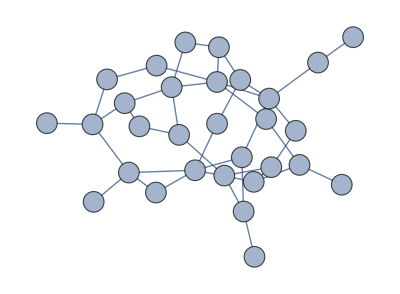

```mathematica
While@Not@ConnectedGraphQ[g=RandomGraph[{30,40},VertexLabels-> Placed[Automatic,Center],VertexSize->1]]
g
```

```mathematica
k=3;

vert=VertexList[g];
absvert=Length[vert];

edge=EdgeList[g];
edge=List @@@%;
absedge=Length[edge];

vertpoly={};
For[i=1,i≤absvert,i++,AppendTo[vertpoly,Indexed[x,i]^k-1]]

vars=Variables[vertpoly];

edgepoly={};
For[i=1,i≤absedge,i++,AppendTo[edgepoly,Part[PolynomialReduce[Indexed[x,Part[Part[edge,i],1]]^k-Indexed[x,Part[Part[edge,i],2]]^k,Indexed[x,Part[Part[edge,i],1]]-Indexed[x,Part[Part[edge,i],2]],{Indexed[x,Part[Part[edge,i],1]],Indexed[x,Part[Part[edge,i],2]]}],1]]];
edgepoly=Flatten[edgepoly];

graphpolyg=Join[vertpoly,edgepoly];

{ggraphtime,ggrob}=AbsoluteTiming[GroebnerBasis[graphpolyg,vars,MonomialOrder->DegreeReverseLexicographic]]
```

$Aborted